## Density distribution

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/maths/markaw/Documents/mpcSim/visualization/density

```mathematica
density=Import["density_269.dat"];
```

```mathematica
nx=density[[1,1]];ny=density[[1,2]];nz=density[[1,3]];
```

```mathematica
rho=Delete[density,1];
```

```mathematica
slices=Partition[rho[[1]],ny*nz];
```

```mathematica
crosssections=Array[cs,nx];
```

{cs[1],cs[2],cs[3],cs[4],cs[5],cs[6],cs[7],cs[8],cs[9],cs[10],cs[11],cs[12],cs[13],cs[14],cs[15],cs[16],cs[17],cs[18],cs[19],cs[20],cs[21],cs[22],cs[23],cs[24],cs[25],cs[26],cs[27],cs[28],cs[29],cs[30]}

```mathematica
Table[crosssections[[i]]=Partition[slices[[i]],nz],{i,1,nx}];
```

```mathematica
Length[%]
```

30

```mathematica
crosssections[[15]]//MatrixForm
```

(0. | 0. | 0. | 6. | 8. | 8. | 7. | 0. | 0. | 0.
0. | 1. | 14. | 11. | 14. | 18. | 19. | 13. | 0. | 0.
0. | 7. | 17. | 14. | 21. | 12. | 22. | 17. | 15. | 0.
4. | 12. | 15. | 15. | 7. | 8. | 21. | 18. | 16. | 6.
7. | 23. | 13. | 16. | 16. | 10. | 14. | 28. | 11. | 7.
5. | 13. | 11. | 14. | 16. | 16. | 11. | 14. | 8. | 6.
2. | 14. | 13. | 13. | 16. | 17. | 19. | 18. | 13. | 6.
0. | 5. | 8. | 13. | 12. | 13. | 17. | 11. | 12. | 0.
0. | 1. | 17. | 22. | 23. | 16. | 12. | 6. | 1. | 0.
0. | 0. | 0. | 4. | 8. | 8. | 4. | 0. | 0. | 0.)

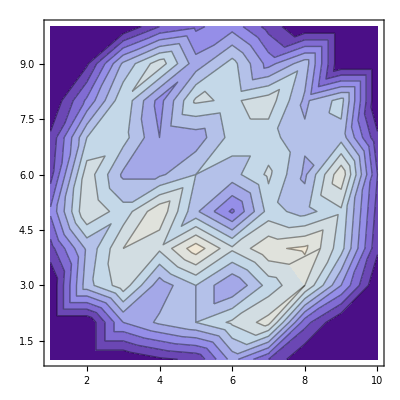

```mathematica
ListContourPlot[crosssections[[2]]]
```

```mathematica
a=1.0;
```

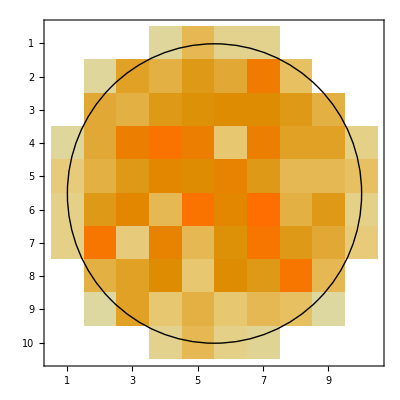

```mathematica
Show[MatrixPlot[crosssections[[10]]],Graphics[Circle[{ny/2,nz/2},(nz-a)/2]]]
```

```mathematica
Mean[crosssections]
```

{{0.,0.,0.,3.8,8.5,7.16667,3.93333,0.,0.,0.},{0.,1.26667,11.0667,15.0333,15.1667,16.4,16.0667,10.1,0.8,0.},{0.,11.2667,15.2667,15.9333,16.5,15.0667,16.0667,16.4667,10.9,0.},{4.03333,15.3667,16.5333,16.8,14.8667,14.3,16.8333,15.9667,16.1,3.9},{6.86667,15.4667,15.5333,15.8667,16.1667,15.7667,16.1667,15.6333,16.4333,7.66667},{7.36667,15.9333,15.7,15.6667,15.7667,15.0333,15.9667,15.1667,16.0667,6.63333},{3.13333,15.1,15.9,15.3,14.6,16.1667,15.4,17.1333,15.5667,4.06667},{0.0333333,12.2333,15.6667,14.9667,14.7667,16.4,14.9,15.2,12.,0.},{0.,1.16667,10.8333,16.7667,15.5333,15.4667,15.2,11.7333,1.2,0.},{0.,0.,0.0333333,3.8,7.9,6.3,3.2,0.,0.,0.}}

```mathematica
MatrixForm[%]
```

(0. | 0. | 0. | 3.8 | 8.5 | 7.16667 | 3.93333 | 0. | 0. | 0.
0. | 1.26667 | 11.0667 | 15.0333 | 15.1667 | 16.4 | 16.0667 | 10.1 | 0.8 | 0.
0. | 11.2667 | 15.2667 | 15.9333 | 16.5 | 15.0667 | 16.0667 | 16.4667 | 10.9 | 0.
4.03333 | 15.3667 | 16.5333 | 16.8 | 14.8667 | 14.3 | 16.8333 | 15.9667 | 16.1 | 3.9
6.86667 | 15.4667 | 15.5333 | 15.8667 | 16.1667 | 15.7667 | 16.1667 | 15.6333 | 16.4333 | 7.66667
7.36667 | 15.9333 | 15.7 | 15.6667 | 15.7667 | 15.0333 | 15.9667 | 15.1667 | 16.0667 | 6.63333
3.13333 | 15.1 | 15.9 | 15.3 | 14.6 | 16.1667 | 15.4 | 17.1333 | 15.5667 | 4.06667
0.0333333 | 12.2333 | 15.6667 | 14.9667 | 14.7667 | 16.4 | 14.9 | 15.2 | 12. | 0.
0. | 1.16667 | 10.8333 | 16.7667 | 15.5333 | 15.4667 | 15.2 | 11.7333 | 1.2 | 0.
0. | 0. | 0.0333333 | 3.8 | 7.9 | 6.3 | 3.2 | 0. | 0. | 0.)

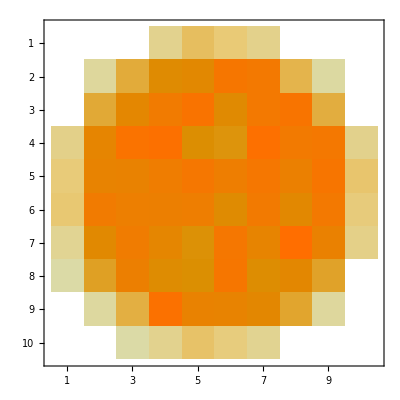

```mathematica
MatrixPlot[%%]
```

```mathematica
ListPlot3D[Mean[crosssections]]
```

-Graphics3D-